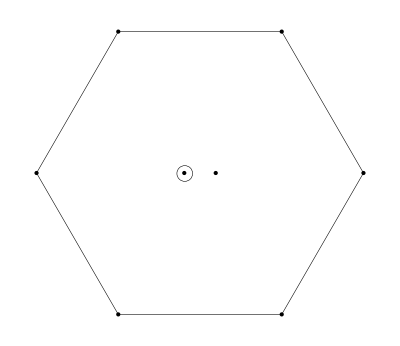

Y=0,  I_3=0

(ud-du)(d̄ū-ūd̄)+(us-su)(ūs̄-s̄ū)

```mathematica
(*-------------------------------*)
```

The current J:

(u_a^T C σ^αμ d_b) ((d̄)_a σ^αμ C((ū)_b)^T-(ū)_a σ^αμ C((d̄)_b)^T)+(d_a^T C σ^αμ u_b) ((ū)_a σ^αμ C((d̄)_b)^T-(d̄)_a σ^αμ C((ū)_b)^T)+(u_a^T C σ^αμ d_b) ((d̄)_b σ^αμ C((ū)_a)^T-(ū)_b σ^αμ C((d̄)_a)^T)+(d_a^T C σ^αμ u_b) ((ū)_b σ^αμ C((d̄)_a)^T-(d̄)_b σ^αμ C((ū)_a)^T)+(s_a^T C σ^αμ u_b-u_a^T C σ^αμ s_b) ((s̄)_a σ^αμ C((ū)_b)^T)+(s_a^T C σ^αμ u_b-u_a^T C σ^αμ s_b) ((s̄)_b σ^αμ C((ū)_a)^T)+(u_a^T C σ^αμ s_b-s_a^T C σ^αμ u_b) ((ū)_a σ^αμ C((s̄)_b)^T)+(u_a^T C σ^αμ s_b-s_a^T C σ^αμ u_b) ((ū)_b σ^αμ C((s̄)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
12 (ū(γ̄)^5 u) (s̄(γ̄)^5 s-d̄(γ̄)^5 d)+12 (ū 1u) (s̄ 1s-d̄ 1d)+12 (d̄(γ̄)^5 u ū(γ̄)^5 d)-2 (d̄ σ^μν d ū σ^μν u)+2 (d̄ σ^μν u ū σ^μν d)+12 (d̄ 1u ū 1d)-12 (s̄(γ̄)^5 u ū(γ̄)^5 s)+2 (s̄ σ^μν s ū σ^μν u)-2 (s̄ σ^μν u ū σ^μν s)-12 (s̄ 1u ū 1s)
```

Π(q^2)=
-(146 log(-q^2/μ^2) ⟨ d̄ d⟩ ⟨ d̄ Gd⟩)/(9 π^2)+(146 log(-q^2/μ^2) ⟨ s̄ s⟩ ⟨ d̄ Gd⟩)/(9 π^2)+(146 log(-q^2/μ^2) ⟨ d̄ d⟩ ⟨ s̄ Gs⟩)/(9 π^2)+(⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(3 π^2 q^2)-⟨ d̄ Gd⟩^2/(6 π^2 q^2)+(64 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(π q^2)-(32 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(π q^2)-(4 q^4 m_d log(-q^2/μ^2) ⟨ d̄ d⟩)/π^4+(1536 m_u ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/q^2-(1792 m_d ⟨ d̄ d⟩ ⟨ ū u⟩^2)/(3 q^2)-(1792 m_u ⟨ d̄ d⟩^2 ⟨ ū u⟩)/(3 q^2)-(96 q^2 log(-q^2/μ^2) ⟨ d̄ d⟩^2)/π^2+(192 q^2 log(-q^2/μ^2) ⟨ d̄ d⟩ ⟨ s̄ s⟩)/π^2-(146 log(-q^2/μ^2) ⟨ s̄ s⟩ ⟨ s̄ Gs⟩)/(9 π^2)-⟨ s̄ Gs⟩^2/(6 π^2 q^2)-(292 log(-q^2/μ^2) ⟨ ū u⟩ ⟨ ū Gu⟩)/(9 π^2)-⟨ ū Gu⟩^2/(3 π^2 q^2)-(32 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(π q^2)-(64 ⟨ GG ⟩ ⟨ ū u⟩^2)/(π q^2)-(4 q^4 m_s log(-q^2/μ^2) ⟨ s̄ s⟩)/π^4-(1792 m_s ⟨ s̄ s⟩ ⟨ ū u⟩^2)/(3 q^2)-(1792 m_u ⟨ s̄ s⟩^2 ⟨ ū u⟩)/(3 q^2)-(8 q^4 m_u log(-q^2/μ^2) ⟨ ū u⟩)/π^4-(96 q^2 log(-q^2/μ^2) ⟨ s̄ s⟩^2)/π^2-(192 q^2 log(-q^2/μ^2) ⟨ ū u⟩^2)/π^2+(2 q^2 log(-q^2/μ^2) ⟨G^3⟩)/π^6-(11 q^4 log(-q^2/μ^2) ⟨ GG ⟩)/(6 π^5)-(q^8 log(-q^2/μ^2))/(40 π^6)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=η_8=η_10=1

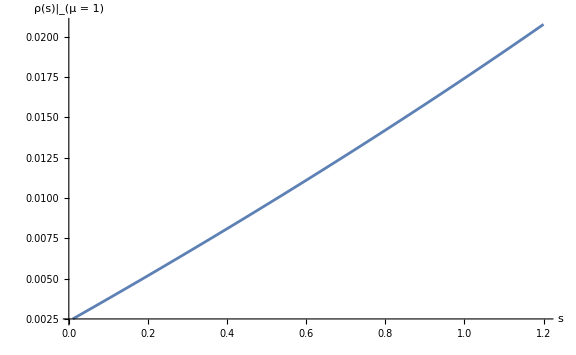
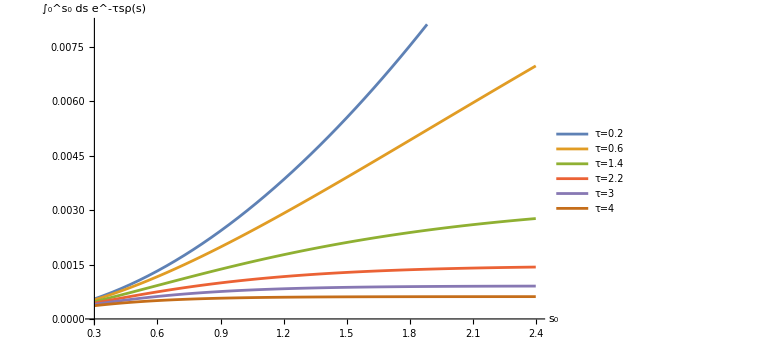

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=η_8=η_10=1

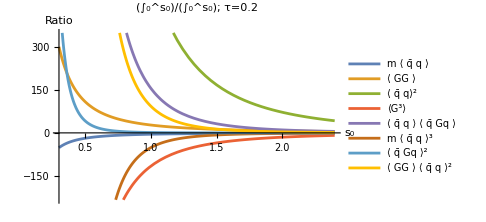
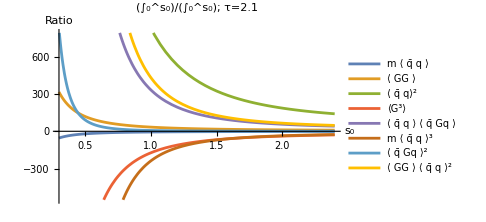
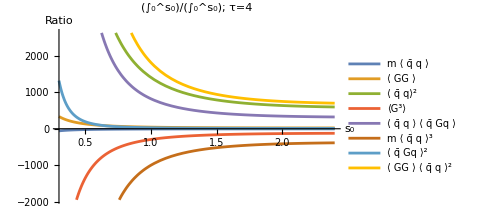

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=η_8=η_10=1

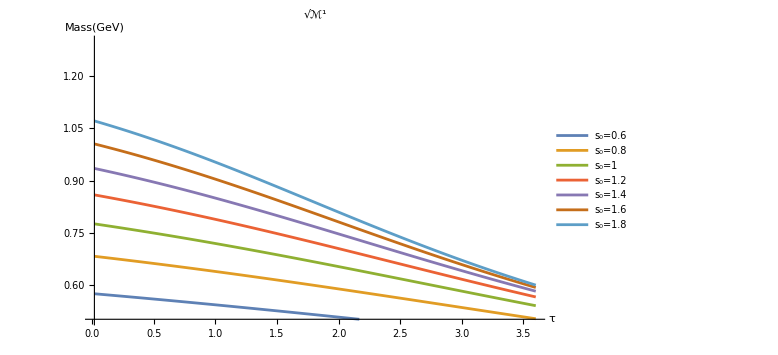
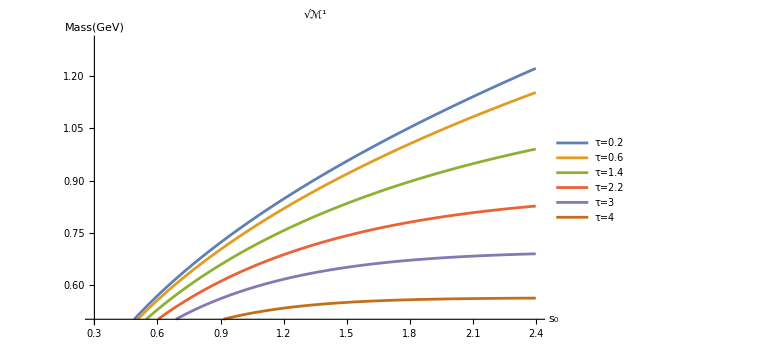

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=η_8=η_10=1

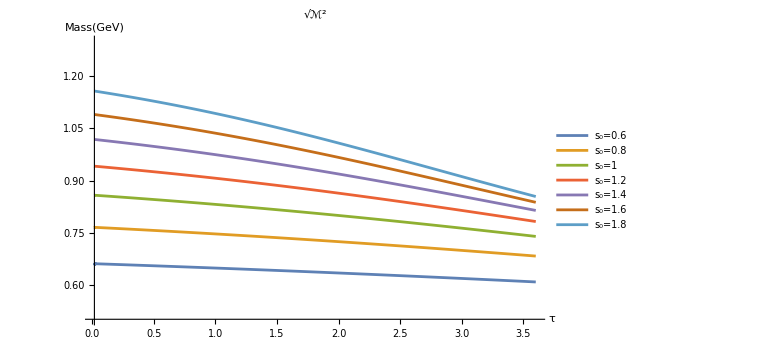
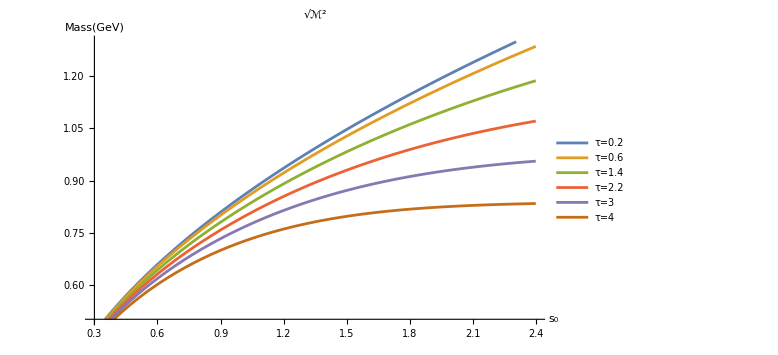

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=3, η_8=5, η_10=5

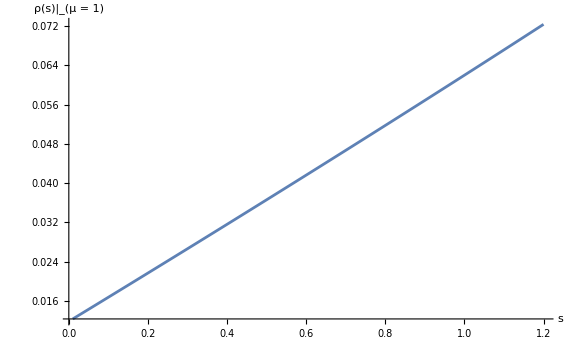
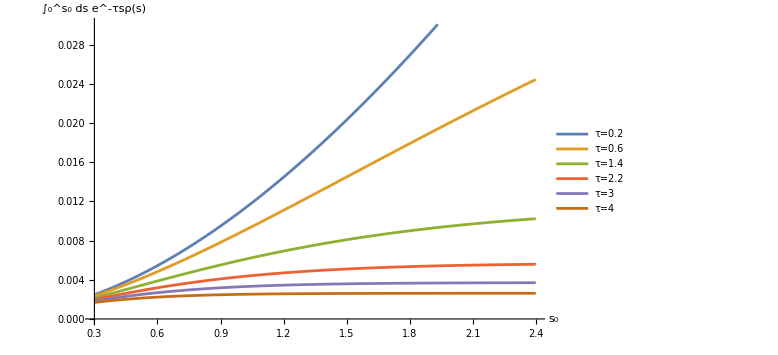

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=3, η_8=5, η_10=5

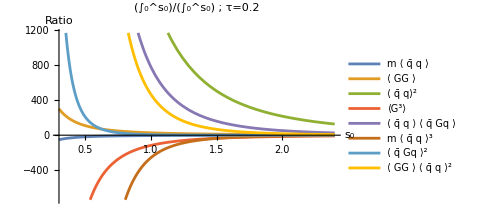
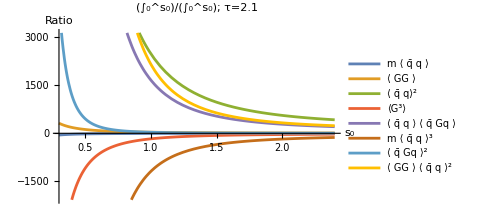
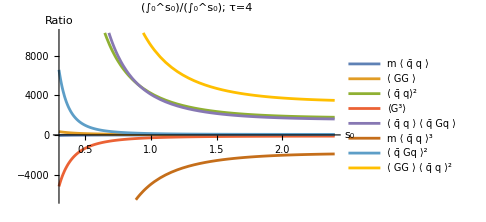

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=3, η_8=5, η_10=5

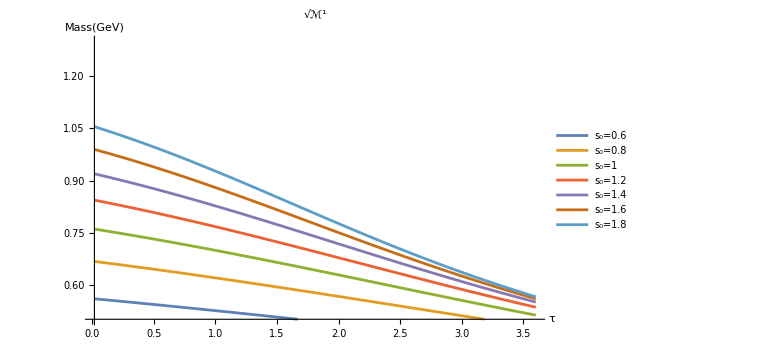
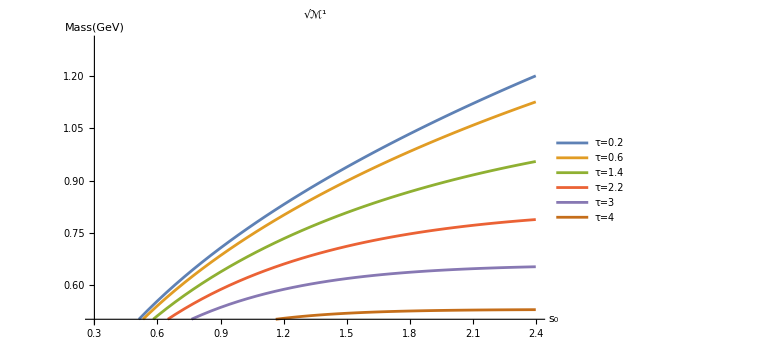

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=3, η_8=5, η_10=5